```mathematica
max=Maximize[{1/10p + 1/20n, p+n≤100, p≥30, n≥1/4(p+n),n≥0},{p,n}]
```

{35/4,{p→75,n→25}}

```mathematica
{35/4,{p->75,n->25}}
```

```mathematica
c= -{1/10,1/20}
```

{-1/10,-1/20}

```mathematica
m={{30,0},{-1,3},{-1,-1}}
```

{{30,0},{-1,3},{-1,-1}}

```mathematica
b={30,0,-100};
```

```mathematica
LinearProgramming[c,m,b]
```

{75,25}

```mathematica
-c.%
```

```mathematica
35/4
```

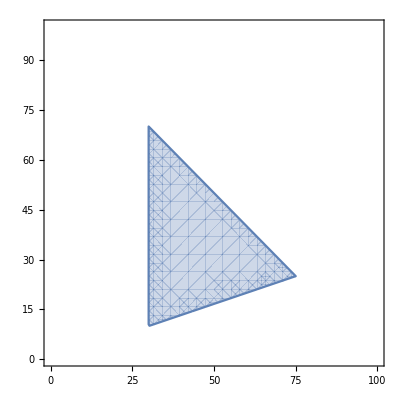

```mathematica
slika1=RegionPlot[{p+n≤100 && p≥30 && n≥1/4(p+n) && n≥0},{p,0,100},{n,0,100}]
```

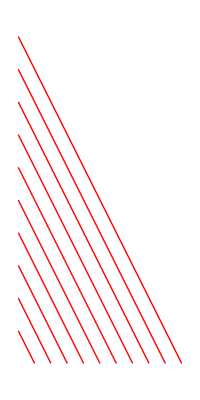

```mathematica
slika2=Graphics[{Red, Table[Line[{{0,20c},{10c,0}}],{c,0,10}]}]
```

```mathematica
max
```

{35/4,{p→75,n→25}}

```mathematica
{p,n}/.max[[2]]
```

{75,25}

```mathematica
slika3=Graphics[{Blue,PointSize[Large],Point[{p,n}/.max[[2]]]}];
```

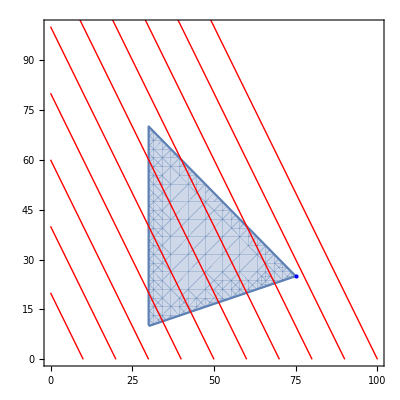

```mathematica
Show[slika1, slika2, slika3]
```

2. primer

```mathematica
Minimize[Abs[x+y-1]+2Abs[3x-2y-7]+3Abs[x+2y+5],{x,y}]
```

{13/4,{x→1/2,y→-11/4}}

```mathematica
c={0,0,0,0,1,2,3};
m={{1,-1,1,-1,-1,0,0},{3,-3,-2,2,0,-1,0},{1,-1,2,-2,0,0,-1}};
b={1,7,-5};
```

```mathematica
slv=LinearProgramming[c,Join[m,-m],Join[b,-b]]
```

{9/5,0,0,4/5,0,0,26/5}

```mathematica
c.slv
```

78/5